```mathematica
Needs["dsvsolve`"];
```

## Input

Edit or simply evaluate the following cell to see the input

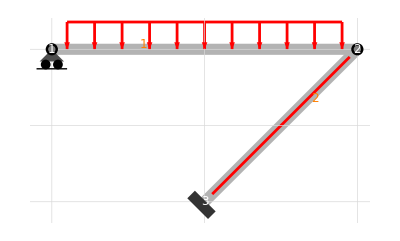

```mathematica
example={$$nodes->{{-2*L, L}, {2*L, L}, {0, -L}},
$$edges->{{1, 2}, {2, 3}},$$absname->s,
$$constraints->{{{"rollh", 1}}, {{"hinge", 1, 2}}, {{"clamp", 2}}},
$$bodyloads->{{1, {0, -q, 0}}},
$$nodalloads->{{1, {0, 0, 0}}},
$$predeformations->{{1, {0, 0, 0}}},
$$cdisplacements->{{1, {0, 0, 0}}},
$$EIoverEAL2->0};
(*All constraints are initialized to hinge constraints; use "BFConstraintsPalette[BFConstraintTypes];" to input different constraints.*)
BFShowInput[example]
```

## Output

Evaluate the following cell to solve the problem and see the output

```mathematica
BFClassify[example]; sol = {{Ns, Qs, Ms}, details} = BFForcesSolve[example];
(*A=Transpose[First[BFStaticProblem[example]]];MatrixForm[A]
BFShowRigidMotions[example]*)
(*BFEquations[example,"Nodal"]; sol = {{us, vs}, {Ns, Qs, Ms}, details} = BFDisplacementsSolve[example];*)
gsol=BFShowOutput[example, sol]
```

BFClassify::sd: Statically determined system.

BFClassify::kd: Kinematically determined system.

123

Evaluate the following cell to print the above output

```mathematica
CellPrint/@Rest/@Last[sol];
Print/@Cases[gsol,Graphics[___],Infinity];
```

Dimensionless abscissa

s

Static equilibrium matrix

{{-1,0,0,1,0,0,0,0,0,0,0,0},{0,-1,0,0,1,0,0,0,0,0,0,0},{0,0,-1,0,4 L,1,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,1,0,0},{0,0,0,0,0,0,0,-1,0,0,1,0},{0,0,0,0,0,0,0,0,-1,0,2 √2 L,1},{1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,-2,0,0,-√2,√2,0,0,0,0},{0,0,0,0,-2,0,-√2,-√2,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,-1,0,0,0,0,0,0}}

Static equilibrium vector

{0,4 L q,8 L^2 q,0,0,0,0,0,0,0,0,0}

Fredholm condition: are the loads orthogonal to allowed rigid motions?

True

Degree of static undetermination

0

Reactions

{{0,-2 L q,0,0,2 L q,0},{-√2 L q,-√2 L q,0,-√2 L q,-√2 L q,4 L^2 q}}

Internal actions (N,Q,M)

{{0,-√2 L q},{-2 L q+4 L q s,-√2 L q},{2/3 L s (12 L q-12 L q s),4 L^2 q s}}

-Graphics-

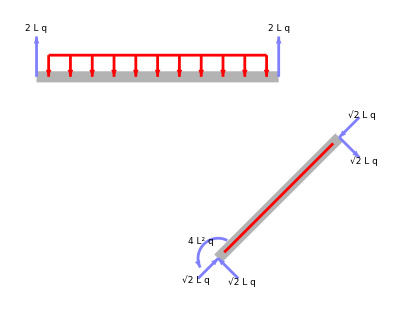

-Graphics-

-Graphics-

-Graphics-